# Lógica 3

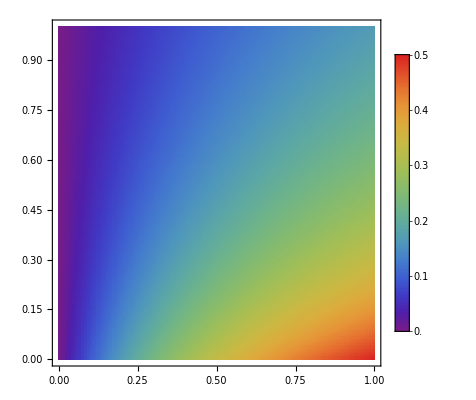

```mathematica
f[A_,R_]:=a Subscript[K, 4]((A Subscript[K, 1]+Subscript[K, 2]+R Subscript[K, 5])/(((R Subscript[K, 3]+Subscript[K, 4]) (Subscript[K, 2]+R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]))-(Subscript[K, 2]+R Subscript[K, 5])/(((R Subscript[K, 3]+Subscript[K, 4]) (Subscript[K, 2]+R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5])));
Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
a = 1;
DensityPlot[f[A,R],{A,0,1},{R,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 4

```mathematica
f[R_,A_]:=(a Subscript[K, 4] (A Subscript[K, 1]+Subscript[K, 2]+R Subscript[K, 5]))/(-((R Subscript[K, 3]+Subscript[K, 4]) (-Subscript[K, 2]-R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]))+(a Subscript[K, 4] (-Subscript[K, 2]-R Subscript[K, 5]))/(-((R Subscript[K, 3]+Subscript[K, 4]) (-Subscript[K, 2]-R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
a = 1;

DensityPlot[f[A,R],{A,0,1},{R,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 14

```mathematica
f[A_,R_]:=a-(a Subscript[K, 4] (A Subscript[K, 1]+Subscript[K, 2]+R Subscript[K, 5]))/(-((R Subscript[K, 3]+Subscript[K, 4]) (-Subscript[K, 2]-R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]))-(a Subscript[K, 4] (-Subscript[K, 2]-R Subscript[K, 5]))/(-((R Subscript[K, 3]+Subscript[K, 4]) (-Subscript[K, 2]-R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
a = 1;

DensityPlot[f[A,R],{A,0,1},{R,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 7

```mathematica
f[A_,B_]:=Subscript[r, 1]((a A)/((1+A) (1+B)))+Subscript[r, 2]((a B)/((1+A) (1+B)))-Subscript[r, 3]((a (A*B))/((1+A) (1+B)));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
Subscript[K, 6]=1;
Subscript[K, 7]=1;
Subscript[K, 8]=1;
a = 1;
Subscript[r, 1]=1;
Subscript[r, 2]=1;
Subscript[r, 3]=2;

DensityPlot[f[A,R],{A,0,1},{R,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 10

```mathematica
f[A_,B_]:=a-(Subscript[r, 1]((a A)/((1+A) (1+B)))+Subscript[r, 2]((a B)/((1+A) (1+B)))-Subscript[r, 3]((a (A*B))/((1+A) (1+B))));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
Subscript[K, 6]=1;
Subscript[K, 7]=1;
Subscript[K, 8]=1;
a = 1;
Subscript[r, 1]=1;
Subscript[r, 2]=1;
Subscript[r, 3]=2;

DensityPlot[f[A,R],{A,0,1},{R,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 15

```mathematica
f[A_,B_]:=a-a*(A^n/(A^n+Subscript[K, a]^n))*(B^n/(B^n+Subscript[K, b]^n));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
Subscript[K, 6]=1;
Subscript[K, 7]=1;
Subscript[K, 8]=1;
a = 1;
Subscript[r, 1]=1;
Subscript[r, 2]=1;
Subscript[r, 3]=2;
Subscript[K, a]=0.5;
Subscript[K, b]=0.5;
n=2;

DensityPlot[f[A,B],{A,0,1},{B,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Lógica 5

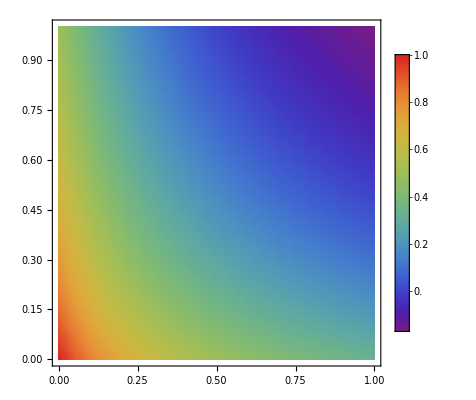

```mathematica
f[A_,B_]:=a-a*((A^n/(A^n+Subscript[K, a]^n))+(B^n/(B^n+Subscript[K, b]^n)));

Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
Subscript[K, 6]=1;
Subscript[K, 7]=1;
Subscript[K, 8]=1;
a = 1;
Subscript[r, 1]=1;
Subscript[r, 2]=1;
Subscript[r, 3]=2;
Subscript[K, a]=0.5;
Subscript[K, b]=1;
n=1;

DensityPlot[f[A,B],{A,0,1},{B,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

# Análisis para lógica 3

```mathematica
f[A_,R_]:=a Subscript[K, 4]((A Subscript[K, 1]+Subscript[K, 2]+R Subscript[K, 5])/(((R Subscript[K, 3]+Subscript[K, 4]) (Subscript[K, 2]+R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5]))-(Subscript[K, 2]+R Subscript[K, 5])/(((R Subscript[K, 3]+Subscript[K, 4]) (Subscript[K, 2]+R Subscript[K, 5]))+A Subscript[K, 1] (Subscript[K, 4]+R Subscript[K, 5])));
Subscript[K, 1]= 1;
Subscript[K, 2]= 1;
Subscript[K, 3]= 1;
Subscript[K, 4]= 1;
Subscript[K, 5]=1;
a = 1;
```

## Coherente 1

```mathematica
f[X_]:= X^n/(X^n+Subscript[K, x]^n);
f[Y_]:= Y^n/(Y^n+Subscript[K, y]^n);
Subscript[K, x] = 0.8;
Subscript[K, y] =0.8;

DensityPlot[f[f[X],f[Y]],{X,0,1},{Y,0,1},PlotPoints->100,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

## Coherente 2

## Coherente 3

## Coherente 4

## Incoherente 1

## Incoherente 2

## Incoherente 3

## Incoherente 4